```mathematica
Clear["Global`*"]
```

## Simple Model

Simple force balance

```mathematica
σ= η D[v[x,t], x] + T;
eqσ :=(D[σ,x]==γ v[x,t])
```

```mathematica
sol=DSolve[{γ v[x]==η v''[x], v[0]==0, v'[L]==0}, v[x], x];
Simplify[v[x]/.sol]
```

{Piecewise[{{-2 C[1] Sinh[(x √γ)/(√η)], (ⅇ^(-(L √γ)/(√η)) (1+ⅇ^((2 L √γ)/(√η))) √γ)/(√η)==0}, {0, True}}]}

Mechanical feedback

```mathematica
e = Δe  ϕ[x,t]+eM(*eO ϕ [x,t]+ eM (1-ϕ[x,t]);*)
kD = α(e-eM);
Simplify[kD]
```

eM+Δe ϕ[x,t]

α Δe ϕ[x,t]

Differentiation dynamics

```mathematica
eqϕ:=Simplify[D[ϕ[x,t],t]+v[x,t] ϕ[x,t]==kD (1-ϕ[x,t])]
eqϕ
```

v[x,t] ϕ[x,t]+α Δe (-1+ϕ[x,t]) ϕ[x,t]+ϕ^(0,1)[x,t]==0

Parameters for numerical solutions

```mathematica
params ={η-> 10000/3600,γ->5/18, α-> 2/10^5, Δe->1000, ΔT->0.1, a->4};
L=1500;
tmax=4;
Nx=200;
T=100;
```

Boundary conditions & IVs

```mathematica
ϕ0[x_]:=(1-Tanh[a x/L])/2;
iv={ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;

bcV ={v[-L,t]==0,Derivative[1,0][v][L,t]==0};
bcϕ={ϕ[-L,t]==1,ϕ[L,t]==0};
bcϕ={ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L]};
```

## Solve model

#### Case 1 A

η constant, T constant
Then v=0 is the only solution.

```mathematica
Clear[T];
eqσ
```

η v^(2,0)[x,t]==γ v[x,t]

#### Case 1B

η constant, T depends on ϕ
Adding an active tension T seems to give problems with NDSolve.

```mathematica
T =ΔT ϕ[x,t]+TM (*TO ϕ[x,t] +TM (1-ϕ[x,t]); *)
eqσ
```

TM+ΔT ϕ[x,t]

ΔT ϕ^(1,0)[x,t]+η v^(2,0)[x,t]==γ v[x,t]

```mathematica
PDEsys0=Flatten@{eqσ, eqϕ, bcV, bcϕ};
PDEsys=Flatten@{eqσ, eqϕ, bcV, bcϕ, iv}
```

{ΔT ϕ^(1,0)[x,t]+η v^(2,0)[x,t]==γ v[x,t],v[x,t] ϕ[x,t]+α Δe (-1+ϕ[x,t]) ϕ[x,t]+ϕ^(0,1)[x,t]==0,v[-1500,t]==0,v^(1,0)[1500,t]==0,ϕ[-1500,t]==1/2 (1+Tanh[a]),ϕ[1500,t]==1/2 (1-Tanh[a]),ϕ[x,0]==1/2 (1-Tanh[x/375]),v[x,0]==0}

```mathematica
(*DSolve[PDEsys0, {v[x,t], ϕ[x,t]}, {x,t}]*)
```

```mathematica
PDEsys /. params
```

{0.1 ϕ^(1,0)[x,t]+25/9 v^(2,0)[x,t]==5/18 v[x,t],v[x,t] ϕ[x,t]+1/50 (-1+ϕ[x,t]) ϕ[x,t]+ϕ^(0,1)[x,t]==0,v[-1500,t]==0,v^(1,0)[1500,t]==0,ϕ[-1500,t]==1/2 (1+Tanh[4]),ϕ[1500,t]==1/2 (1-Tanh[4]),ϕ[x,0]==1/2 (1-Tanh[x/375]),v[x,0]==0}

```mathematica
ndsol=NDSolve[PDEsys /. params, {v[x,t], ϕ[x,t]}, {x,-L,L},{t,0,tmax},Method->{"EquationSimplification"->"Residual","IndexReduction"->Automatic}]
```

NDSolve::ndcf: Repeated convergence test failure at t == 0.0001; unable to continue.

{{v[x,t]→InterpolatingFunction[…][x,t],ϕ[x,t]→InterpolatingFunction[…][x,t]}}

InterpolatingFunction::dmval: Input value {-1499.79,0.000285714} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

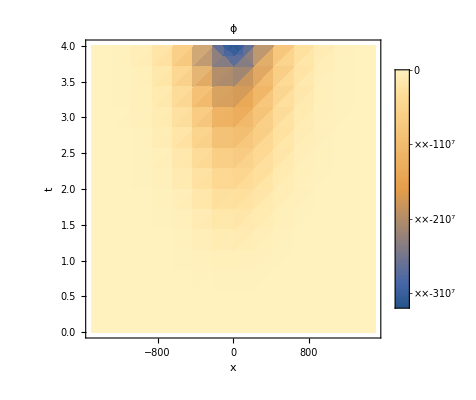
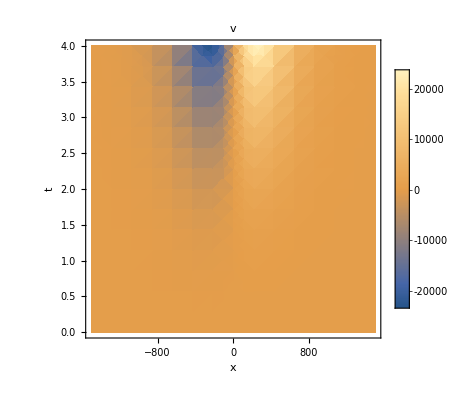

```mathematica
{DensityPlot[ϕ[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"ϕ"],
DensityPlot[v[x,t]/.ndsol[[1]],{x,-L,L},{t,0,tmax},Mesh->None,PlotRange-> All,AxesLabel->Automatic,PlotLegends->Automatic, PlotLabel->"v"]}
```

### ODE for v[x]

Solution blows up as soon as |T|>0.
Also true if ϕ[x] = constant.

#### DSolve

Space dependent ϕ[x] gives a very complicated analytic solution.

```mathematica
Clear[L]
odeV=(ΔT ϕ[x]+η v''[x]==γ v[x]);
odeBC = {v[-L]==0,v'[L]==0};
odeSys=Flatten[{odeV,odeBC}]
odesol=DSolve[odeSys, v[x], {x,-L,L}];
v[x]/.odesol
```

{ΔT ϕ[x]+η v''[x]==γ v[x],v[-L]==0,v'[L]==0}

DSolve::alliv: The function v[x] was specified without dependence on all the independent variables. Each function must depend on all the independent variables.

ReplaceAll::reps: {DSolve[{ΔT ϕ[x]+η v''[x]==γ v[x],v[-L]==0,v'[L]==0},v[x],{x,-L,L}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[x]/.DSolve[{ΔT ϕ[x]+η v''[x]==γ v[x],v[-L]==0,v'[L]==0},v[x],{x,-L,L}]

```mathematica
FullSimplify[v[x]/.odesol]
```

$Aborted

Constant ϕ[x] gives a more reasonable analytic solution.

```mathematica
odeV=(ΔT+η v''[x]==γ v[x]);
odeBC = {v[-L]==0,v'[L]==0};
odeSys=Flatten[{odeV,odeBC}]
odesol=DSolve[odeSys, v[x], {x}];
v[x]/.odesol
```

{ΔT+η v''[x]==γ v[x],v[-L]==0,v'[L]==0}

{-(ⅇ^(-(x √γ)/(√η)) (-ⅇ^((4 L √γ)/(√η)+(x √γ)/(√η))+ⅇ^((L √γ)/(√η)+(2 x √γ)/(√η))+ⅇ^((3 L √γ)/(√η))-ⅇ^((x √γ)/(√η))) ΔT)/((1+ⅇ^((4 L √γ)/(√η))) γ)}

```mathematica
vsol=Simplify[v[x]/.First@odesol]
```

((1+ⅇ^((4 L √γ)/(√η))-ⅇ^(((3 L-x) √γ)/(√η))-ⅇ^(((L+x) √γ)/(√η))) ΔT)/((1+ⅇ^((4 L √γ)/(√η))) γ)

```mathematica
Sqrt[γ/η]L/.paramsODE
```

150 √10

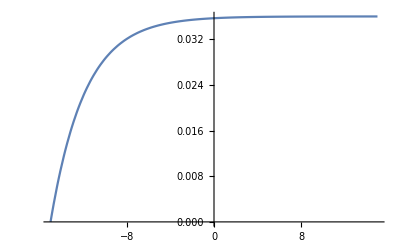

```mathematica
L=15;
Plot[vsol /. paramsODE, {x,-L, L}, PlotRange->Full]
```

#### NDSolve

```mathematica
paramsODE={η-> 10000/3600,γ->5/18,ΔT->0.01,a->4};
L=1500;
odeSys/.paramsODE
odeSys/.{ϕ[x]-> ϕ0[x]}/.paramsODE
```

{0.01 ϕ[x]+(25 v''[x])/9==(5 v[x])/18,v[-1500]==0,v'[1500]==0}

{0.005 (1-Tanh[x/375])+(25 v''[x])/9==(5 v[x])/18,v[-1500]==0,v'[1500]==0}

```mathematica
(*odendsol=NDSolve[odeSys/.{ϕ[x]-> ϕ0[x]}/.paramsODE, v[x], {x,-L,L}];*)
odendsol=NDSolve[odeSys/.{ϕ[x]-> 1}/.paramsODE, v[x], {x,-L,L}];
odendsol
```

General::munfl: 1/(5.0419×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.87238×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.83964×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 3.2979×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

{{v[x]→InterpolatingFunction[…][x]}}

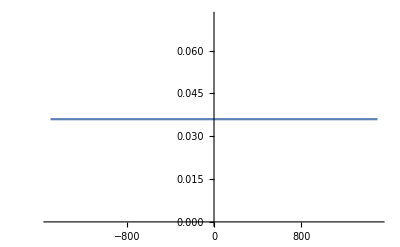

```mathematica
Plot[ v[x]/.odendsol, {x,-L,L}]
```

## Plot Solution

#### NDSolve

#### Discrete mesh

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full};

plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{ pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

Table::iterb: Iterator {j,1,T+1} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,ϕAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,ϕAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Table::iterb: Iterator {j,1,T+1} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {j,1,T+1} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,VAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,VAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Table::iterb: Iterator {j,1,T+1} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,ϕAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

Part::pkspec1: The expression i cannot be used as a part specification.

ListDensityPlot::arrayerr: Table[{xmesh⟦i⟧,tmesh⟦j⟧,VAll⟦i,j⟧},{i,1.,201.},{j,1.,T+1.}] must be a valid array.

General::stop: Further output of ListDensityPlot::arrayerr will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-